## V evolution across the four fitting approaches

## Step for the MOI: 1

```mathematica
vvalues={1.8,1.8,5.3,5.3};
```

```mathematica
vPlot[values_]:=ListPlot[values,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,PlotRange->{{0.8,4.2},{1,6}},FrameStyle->Directive[Thick,Black],FrameLabel->{"","V [MeV]"},LabelStyle->{20,Black,Bold,FontFamily->"Times New Roman"},FrameTicks->{Automatic,{{{1,"A1"},{2,"A2"},{3,"B1"},{4,"B2"}},None}},Epilog->{Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.5,0.25}]],Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.9,0.75}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.68,0.75}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.10,0.25}]]},ImageSize->Large];
```

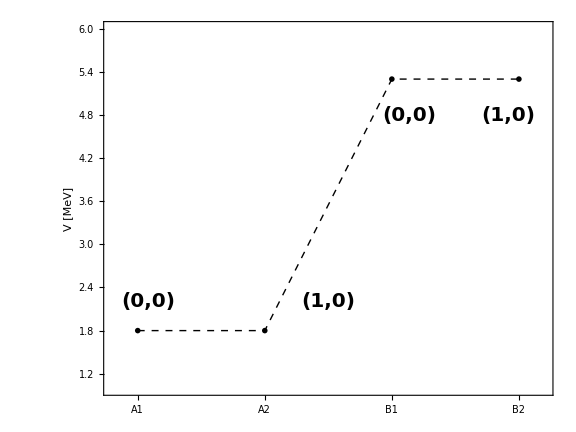

```mathematica
Show[vPlot[vvalues]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/V_evolution.png",Show[vPlot[vvalues]]];
```